Data file Importing:

```mathematica
AppendTo[$Path,"Desktop/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"/Users/emulder/GitHub/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"/Users/iliparti/PhotonInterferenceLab/Analysis"];
data2Slit = Import["4.45mmAll.csv"];
dataFarSlit = Import["4mmAll.csv"];
dataNearSlit = Import["5.9mmAll.csv"];
data2SlitAvg = Import["4.45mmAvg.csv"];
dataFarSlitAvg = Import["4mmAvg.csv"];
dataNearSlitAvg = Import["5.9mmAvg.csv"];
data2SlitErr = Import["4.45mmError.csv"];
dataFarSlitErr = Import["4mmError.csv"];
dataNearSlitErr = Import["5.9mmError.csv"];
dataDouble=Import["just_values_double.csv"];
```

```mathematica
Needs["ErrorBarPlots`"]
```

Fraunhofer Model for double slit and single slit: fit comparison with data and parameter optimization

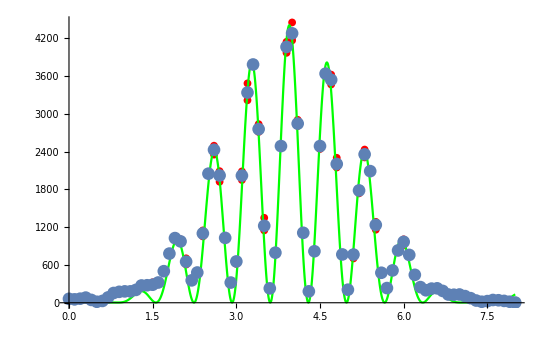

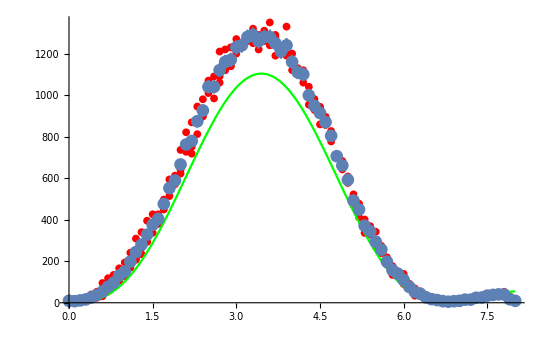

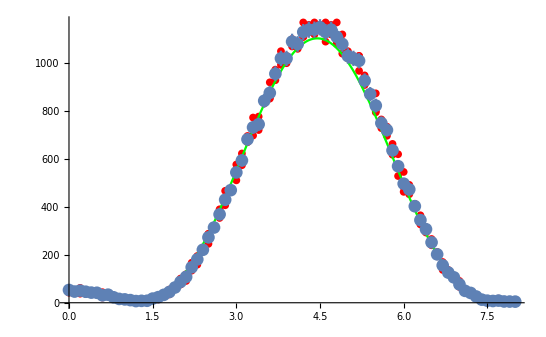

```mathematica
g[x_]:= I0*((Sin[Pi*a*Sin[(x-x0)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/D2])))^2)*(Cos[Pi*d*Sin[(x-x0)/D2]/lambda]^2)+c;
I0 = 4400;
a = 0.085;
d = 0.406;
lambda = 0.000555;
x0 = 3.95;
c = 3.6;
D1=338;
D2=500;
fit = Plot[g[x],{x,0,8},PlotStyle->Green];
dataPlot2Slit =ListPlot[data2Slit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataPlot2SlitAvg=ErrorListPlot[Table[{data2SlitAvg[[i]],ErrorBar[.01,Flatten[data2SlitErr][[i]]]},{i,81}]];
Show[dataPlot2Slit,fit,dataPlot2SlitAvg]

h[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x1)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x1)/D2])))^2)+c;
x1 = 3.45;
fit2 = Plot[h[x],{x,0,8},PlotRange->All,PlotStyle->Green];
dataPlotFarSlit = ListPlot[dataFarSlit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataPlotFarSlitAvg=ErrorListPlot[Table[{dataFarSlitAvg[[i]],ErrorBar[.01,Flatten[dataFarSlitErr][[i]]]},{i,81}]];
Show[dataPlotFarSlit,fit2,dataPlotFarSlitAvg]

k[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x2)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x2)/D2])))^2)+c;
x2 = 4.45;
fit3 = Plot[k[x],{x,0,8},PlotRange->All,PlotStyle->Green];
dataPlotNearSlit = ListPlot[dataNearSlit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataPlotNearSlitAvg = ErrorListPlot[Table[{dataNearSlitAvg[[i]],ErrorBar[.01,Flatten[dataNearSlitErr][[i]]]},{i,81}]];
Show[dataPlotNearSlit,fit3,dataPlotNearSlitAvg]
```

Fresnel Model for double slit and single slit: fit comparison with data and parameter optimization

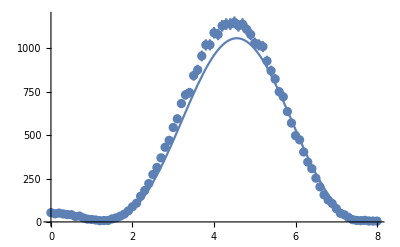

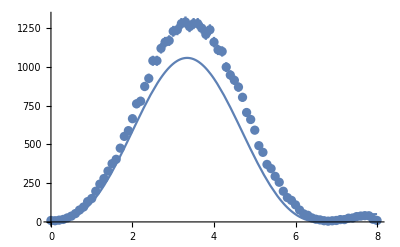

```mathematica
slit1[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0+(d/2),x0+(d/2)+a}]
s1[z_]:=33.3*I0*Re[slit1[z]*Conjugate[slit1[z]]]
slit2[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0-(d/2)-a,x0-(d/2)}]
s2[z_]:=33.3*I0*Re[slit2[z]*Conjugate[slit2[z]]]
fitb=Plot[s1[z],{z,0,8},PlotRange->All];
fitc=Plot[s2[z],{z,0,8},PlotRange->All];
Show[fitb,dataPlotNearSlitAvg]
Show[fitc,dataPlotFarSlitAvg]
```

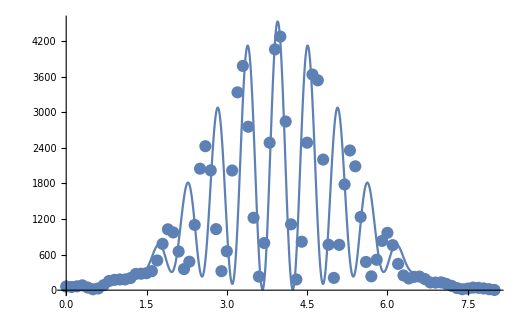

```mathematica
slitdouble[z_]:=slit1[z]+slit2[z]
slit[z_]:=40*I0*Re[slitdouble[z]*Conjugate[slitdouble[z]]]
fita=Plot[slit[z],{z,0,8}];
Show[fita,dataPlot2SlitAvg]
```

```mathematica
PearsonChiSquareTest[Table[data2SlitAvg[i],slit[i],{i,80}]]
```

```mathematica
Table[Flatten[dataDouble][[i]],slit[i/10],{i,0,80,1}]
```

Table::itform: Argument slit[i/10] at position 2 does not have the correct form for an iterator.

```mathematica
Table[{Flatten[dataDouble]⟦k+1⟧,slit[k/10]},{k,0,80,1}]
```

{{62.3333,72.5688},{53.6667,51.0971},{64.3333,65.5671},{81.6667,94.7594},{45,77.9795},{15.3333,20.0351},{29,5.00453},{84.3333,80.7272},{154.667,179.051},{173.333,201.499},{180.667,156.56},{180.667,144.275},{204,205.504},{274,268.983},{277.667,290.022},{286.333,357.973},{321.333,556.634},{500.667,753.986},{780.333,700.471},{1026,417.122},{973.667,332.237},{652,810.631},{355.333,1560.15},{480,1783.71},{1100.33,1127.5},{2048.33,319.342},{2427.33,501.402},{2020,1819.03},{1029.33,2991.39},{320.333,2655.43},{655.333,1080.6},{2017.67,106.161},{3335.67,1093.41},{3781,3189.88},{2755.67,4110.87},{1221,2750.49},{228.333,599.794},{794.667,155.419},{2486.33,2036.36},{4060,4186.01},{4275.33,4186.01},{2843.33,2036.36},{1110,155.419},{181,599.794},{817,2750.49},{2486.33,4110.87},{3635.67,3189.88},{3538.33,1093.41},{2202,106.161},{766.333,1080.6},{207,2655.43},{764.333,2991.39},{1782.33,1819.03},{2355.33,501.402},{2088.67,319.342},{1235,1127.5},{476,1783.71},{233,1560.15},{513,810.631},{830.667,332.237},{966.667,417.122},{759,700.471},{443,753.986},{248.333,556.634},{197.667,357.973},{224.333,290.022},{229,268.983},{187.667,205.504},{130.667,144.275},{127.333,156.56},{131,201.499},{105.333,179.051},{72.6667,80.7272},{35,5.00453},{15.6667,20.0351},{26,77.9795},{43.6667,94.7594},{39.6667,65.5671},{29.3333,51.0971},{16.3333,72.5688},{3.33333,81.9372}}